# NG^21 P_09. Метод обратного распространения ошибки

Бельской Екатерины, 
2 курс, 5 группа

## 1. Исходные данные и их стандартизация

{4436,3}

{1100,5}

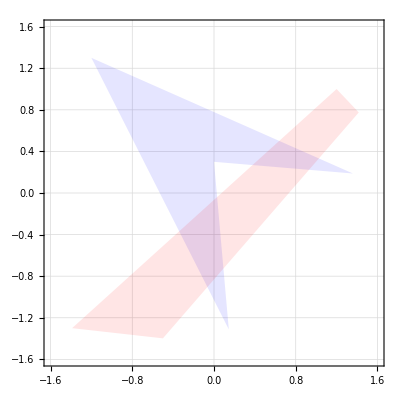

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory";
Dimensions[TrainSet=Import["NG21P09Problem.xlsx",{"Sheets","Train"}]⟦2;;-1⟧]
Dimensions[TestSet=Import["NG21P09Problem.xlsx",{"Sheets","Test"}]⟦2;;-1⟧]
Fig0=Uncompress[Import["NG21P09Problem.xlsx",{"Sheets","Fig0"}]⟦1,1⟧]
```

```mathematica
X=TrainSet⟦All,1;;2⟧;
```

```mathematica
Y=TrainSet⟦All,3⟧;
```

```mathematica
YT=UnitVector[3,IntegerPart@#]&/@TrainSet⟦;;,3⟧;
```

```mathematica
Map[Dimensions,{blue=First[#]&/@Position[TrainSet,1.],
red=First[#]&/@Position[TrainSet, 2.],gray=First[#]&/@Position[TrainSet,3.]}]
```

{{750},{750},{2936}}

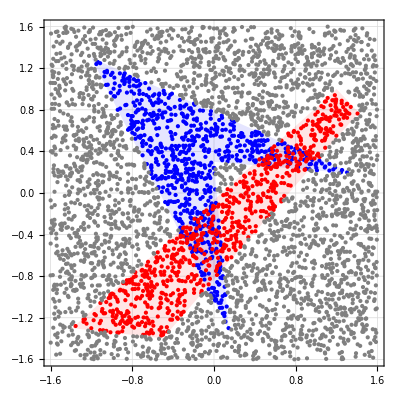

```mathematica
Show[Fig0,Graphics[{Blue,Point@X⟦blue⟧,Red, Point@X⟦red⟧,Gray, Point@X⟦gray⟧},Frame->True,GridLines->Automatic]]
```

## 2. Полносвязная нейронная сеть прямого распространения

```mathematica
ClearAll[LReLU,LReLU1,SoftMax];
LReLU=Function[x,If[0<x,x,.01x],Listable];
LReLU1=LReLU';
SoftMax=#/(Total@#)&@Exp[#]&;
```

```mathematica
ClearAll[kmANN];
kmANN[]:=Set[kmWeight,RandomReal[{-1,1},#]&/@{{9,3},{12,10},{3,13}}]
kmANN[sample_]:=sample//Sow@Append[#,1]&//Sow@Append[LReLU[kmWeight⟦1⟧.#],1]&//Sow@Append[LReLU[kmWeight⟦2⟧.#],1]&//Sow@SoftMax[kmWeight⟦3⟧.#]&
```

```mathematica
kmANN[];
```

## 3. Визуализация

```mathematica
kmEpoch=1;
```

```mathematica
ClearAll[grid];
grid:=Table[kmANN@{j,i},{i,-1.5,1.5,1/20},{j,-1.5,1.5,1/20}];
```

```mathematica
grid//Dimensions
```

{61,61,3}

```mathematica
Graphics[Raster[grid,{{-1.5,-1.5},{1.5,1.5}},ColorFunction->(Blend[{Blue,Red,Gray},#]&)],Frame->True,PlotLabel->StringJoin["epoch: ",ToString@kmEpoch]]
```

-Graphics-

```mathematica
CreatePalette@Dynamic[Show[Graphics[Raster[grid,{{-1.5,-1.5},{1.5,1.5}},ColorFunction->(Blend[{Blue,Red,Gray},#]&)],Frame->True,PlotLabel->StringJoin["epoch: ",ToString@kmEpoch]],Fig0],TrackedSymbols:>{kmEpoch}]
```

g3p2x_shm37FrontEndObject[LinkObject["g3p2x_shm", 3, 1]]37Untitled-7

## 4. Прямой ход обучения

```mathematica
Y=Reap[kmANN[X⟦2⟧]]⟦2,1⟧
```

{{0.101878,-0.52802,1},{0.0191119,0.0261439,-0.000115265,-2.54926×10^-7,0.0194161,0.126212,-0.00093115,-0.000838459,0.0962041,1},{-0.000880858,-0.000509377,-0.000406219,-0.000112697,0.0745291,0.0753889,-0.000732321,0.0879118,0.0537839,-0.000205094,-0.000879451,-0.000763475,1},{0.341024,0.34256,0.316416}}

## 5. Локальные градиенты

```mathematica
ClearAll[kmLoss];
kmLoss[Y_,YT_]:=-YT.RealExponent[Y,ⅇ];
```

```mathematica
Y=Reap[kmANN[X⟦2⟧]]⟦2,1⟧
```

{{0.101878,-0.52802,1},{-0.00110959,0.0910565,0.0356181,0.0554365,-0.000875222,-0.00006538,-0.00129702,0.107584,0.017695,1},{-0.000353169,-0.000895768,-0.000675171,-0.000041144,0.0196555,-0.000104045,-0.000616102,-0.000714933,-0.000287324,-0.000295658,0.0578926,-0.000797652,1},{0.302032,0.362299,0.335669}}

```mathematica
δ=ConstantArray[{},3]
```

{{},{},{}}

```mathematica
δ⟦3⟧=YT⟦2⟧-kmANN[X⟦2⟧]
```

{-0.171111,0.955183,-0.784072}

```mathematica
δ
```

{{0.0154197,0.00426473,-0.00377217,-0.00737784,-0.000509181,-0.00822259,0.00747967,0.00105986,0.00631552},{-0.0241835,-0.0174116,-0.0149184,-0.0521227,0.0156471,0.0597921,-0.0355504,0.0392483,0.0778097,0.00714161,-0.031678,0.0645154},{-0.302032,0.637701,-0.335669}}

```mathematica
Dot[δ⟦3⟧,kmWeight⟦3⟧]
```

{1.55605,0.0603162,-0.0673751,-0.811239,-0.865134,0.385409,0.174649,-0.198078,1.45648,-0.999319,0.181233,0.357977,-0.502593}

```mathematica
δ⟦2⟧=(LReLU'[#]&/@Most[Y⟦3⟧])Most@Dot[δ⟦3⟧,kmWeight⟦3⟧]
```

{1.55605,0.0603162,-0.0673751,-0.811239,-0.865134,0.385409,0.174649,-0.198078,1.45648,-0.999319,0.181233,0.357977}

```mathematica
δ⟦1⟧=(LReLU'[#]&/@Most[Y⟦2⟧])Most@Dot[δ⟦2⟧,kmWeight⟦2⟧]
```

{-2.61414,-1.96069,-1.46165,-2.35766,-0.422988,1.01437,0.397552,3.07484,-1.25324}

```mathematica
Map[Dimensions,ΔW={Outer[Times,δ⟦1⟧,Y⟦1⟧],
Outer[Times,δ⟦2⟧,Y⟦2⟧],Outer[Times,δ⟦3⟧,Y⟦3⟧]}]
```

{{9,3},{12,10},{3,13}}

## 6. Обратный ход обучения

```mathematica
Subscript[ΔW, n, i]:=η Subscript[x, i] Subscript[δ, n]
Subscript[δ, l,n]:=Subscript[ϕ, l]'∑_(m=1)^Subscript[N, l+1] Subscript[w, l+1,m,n] Subscript[δ, l+1,m],n=1,... Subscript[N, l]
Subscript[V, l,n]=Subscript[w, l,0]+∑_(i=1)^Subscript[I, l,n] Subscript[w, l,n,i] Subscript[x, l,i]
Subscript[δ, 3,n]:=Subscript[T, n]-Subscript[Y, 3, n]
```

```mathematica
ClearAll[kmΔWeight];
kmΔWeight[sample_]:=Block[{Y=Reap[kmANN[sample⟦1;;2⟧]]⟦2,1⟧,δ={0,0,0}},
δ⟦3⟧=UnitVector[3,IntegerPart[sample⟦3⟧]]-Last@Y;
δ⟦2⟧=(LReLU'[#]&/@Most[Y⟦3⟧])Most@Dot[δ⟦3⟧,kmWeight⟦3⟧];
δ⟦1⟧=(LReLU'[#]&/@Most[Y⟦2⟧])Most@Dot[δ⟦2⟧,kmWeight⟦2⟧];
{Outer[Times,δ⟦1⟧,Y⟦1⟧],
Outer[Times,δ⟦2⟧,Y⟦2⟧],Outer[Times,δ⟦3⟧,Y⟦3⟧]}
]
```

```mathematica
RandomSample@TrainSet⟦;;20⟧
k=Partition[%,UpTo@10]
```

{{-0.0778419,0.525071,1.},{-0.752585,-0.495197,3.},{1.27039,-1.34245,3.},{-0.557006,-1.56834,3.},{0.101878,-0.52802,2.},{1.09312,-1.01829,3.},{-0.142489,1.32376,3.},{1.53568,-0.9548,3.},{0.215766,0.739392,3.},{1.13003,0.280393,1.},{0.163754,0.477132,1.},{-1.22781,0.941836,3.},{0.684287,1.39161,3.},{-0.595254,0.844415,1.},{0.315499,-0.884736,3.},{0.368988,0.652889,3.},{1.10203,-1.14333,3.},{1.49896,-0.346666,3.},{-1.32691,1.56162,3.},{0.952953,0.560569,2.}}

{{{-0.0778419,0.525071,1.},{-0.752585,-0.495197,3.},{1.27039,-1.34245,3.},{-0.557006,-1.56834,3.},{0.101878,-0.52802,2.},{1.09312,-1.01829,3.},{-0.142489,1.32376,3.},{1.53568,-0.9548,3.},{0.215766,0.739392,3.},{1.13003,0.280393,1.}},{{0.163754,0.477132,1.},{-1.22781,0.941836,3.},{0.684287,1.39161,3.},{-0.595254,0.844415,1.},{0.315499,-0.884736,3.},{0.368988,0.652889,3.},{1.10203,-1.14333,3.},{1.49896,-0.346666,3.},{-1.32691,1.56162,3.},{0.952953,0.560569,2.}}}

```mathematica
kmANN[];
```

```mathematica
Dimensions[(kmWeight+=0.02*Sum[kmΔWeight[sample],{sample,#}])&/@k]
```

{1,3}

```mathematica
Map[Dimensions,kmWeight]
```

{{9,3},{12,10},{3,13}}

```mathematica
kmANN[];
```

Данный вариант с динамическим обновлением почему - то выдает ошибку. Аналогичный вариант без отображения на палитре работает верно

ClearAll[kmTrain];
kmTrain[batch_Integer, η_Real] := Block[{l, batchCounter = Ceiling[Length[TrainSet]/batch], n = 0},
  l = Partition[RandomSample@TrainSet, UpTo@batch];
  Monitor[Scan[(n++; kmWeight += η Sum[kmΔWeight[sample], {sample, #}]) &, l], ProgressIndicator[n, {0, batchCounter}]]
  ]
kmTrain[batch_Integer, η0_Real, epochs_] := Block[{η = η0}, kmEpoch = 0; kmANN[]; Do[η = 0.99 η; kmTrain[batch, η]; kmEpoch++, epochs]]

```mathematica
ClearAll[kmTrain];
kmTrain[batch_Integer,η_Real,epochs_]:=Module[{l,η0=η,batchCounter=Ceiling[Length[TrainSet]/batch]},
Do[l=Partition[RandomSample@TrainSet,UpTo@batch];
(kmWeight+=η0 Sum[kmΔWeight[sample],{sample,#}])&/@l;
η0=.99η0;kmEpoch++,epochs]]
```

## 7. Обучение классификатора

```mathematica
kmEpoch=1;
```

```mathematica
kmANN[];
```

```mathematica
kmTrain[10,0.02,120]
```

```mathematica
Graphics[Raster[grid,{{-1.5,-1.5},{1.5,1.5}},ColorFunction->(Blend[{Blue,Red,Gray},#]&)],Frame->True,PlotLabel->StringJoin["epoch: ",ToString@kmEpoch]]
```

-Graphics-

## 8. Качество обучения

```mathematica
TestSet//Length
```

```mathematica
YT=TestSet⟦;;,3;;5⟧;
```

```mathematica
Position[YT⟦1⟧,1.]
```

```mathematica
Length@TestSet
```

1100

```mathematica
testRes=kmANN[TestSet⟦#,1;;2⟧]&/@Range[Length@TestSet];
```

```mathematica
wrong={};
```

```mathematica
Do[If[Position[testRes⟦i⟧,Max[testRes⟦i⟧]]!=Position[YT⟦i⟧,1.],AppendTo[wrong,i]],{i,Length@TestSet}]
```

```mathematica
Length@wrong
```

56

Процент неверное распознанных данных

```mathematica
N[Length[wrong]/Length[TestSet]]*100
```

5.09091

Среднее значение функции потерь

```mathematica
Total[MapThread[kmLoss[#1,#2]&,{testRes,YT}]]/1100
```

0.0698926